# Mendelian Model Project

This notebook is part two of the final project and will help you with its implementation. It provides the functions from the previous part, as well as function definitions for you to fill out, as well as tests to verify that you’ve written each piece correctly.

If you succeeded in building part 1 by yourself, we recommend that you augment your own code to incorporate the Mendelian model, as you will already be familiar with your own code. Also, we think that you will have a fun time finding ways to generalize your code so that functions you created for the blending model can work equally well with the Mendelian model. That being said, our solution lecture will build off of this file, so if you’d prefer to start in the same place as us, we welcome you to follow along. Good luck!

## Constants

As we did in part 1, we will be drawing our creatures in a 50x50 area:

```mathematica
xmin=0;xmax=50;
ymin=0;ymax=50;
```

The traits in our Blending Model was a number between 0 and 1. The traits of our Mendelian Model however are discrete; so we’ll define them as a list of individual genes:

```mathematica
latinGenes={"A","B","C","D"};
numberGenes={"1","2","3","4"};
```

## Creatures

Part 2 of the project must incorporate both BlendingCreatures and MendelianCreatures. Let’s create a few prototypical creatures of each type that we will make use of in our tests:

```mathematica
bc1=BlendingCreature[0.1,{20,40}];
bc2=BlendingCreature[0.4,{30,40}];
bc3=BlendingCreature[0.7,{40,30}];
bc4=BlendingCreature[0.9,{40,20}];
mc1=MendelianCreature[{"A","1"},{25,45}];
mc2=MendelianCreature[{"B","3"},{35,45}];
mc3=MendelianCreature[{"D","1"},{45,35}];
mc4=MendelianCreature[{"C","4"},{45,25}];
```

## Accessors

In part 1, we wrote the Traits function to work on BlendingCreatures. Write some code to enable Traits to work on both BlendingCreatures and MendelianCreatures.

```mathematica
Traits[creature_BlendingCreature]:=creature[[1]]
```

Our second function gets the location of the creature. Update it to work with MendelianCreatures as well.

```mathematica
Location[creature_BlendingCreature]:=creature[[2]]
```

### Tests

#### Verify the accessors

Here’s our first set of tests. These should evaluate the True if you’ve written your code above correctly!

```mathematica
Traits[bc1]===0.1
```

```mathematica
Traits[bc2]===0.4
```

```mathematica
Location[bc3]==={40,30}
```

```mathematica
Location[bc4]==={40,20}
```

```mathematica
Traits[mc1]==={"A","1"}
```

```mathematica
Traits[mc2]==={"B","3"}
```

```mathematica
Location[mc3]==={45,35}
```

```mathematica
Location[mc4]==={45,25}
```

## Evolution

In part 1, we wrote the Procreate function to evolve two BlendingCreatures by blending their traits. Here is the implementation:

```mathematica
Procreate[mother_BlendingCreature,father_BlendingCreature,OptionsPattern[{ChildCount->1}]]:=
Table[
BlendingCreature[
Mean[{Traits[father],Traits[mother]}],
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],
OptionValue[ChildCount]]
```

Now we need to create a Procreate function that will evolve two MendelianCreatures. In the Blending Model, we would take the average of the traits of the father and mother. In the Mendelian Model, we must pick between discrete genes from the father and mother. So, for example, if the father’s traits are {“A”, “1”} and the mother’s traits are {“C”, “4”}, then the child can be any of {{“A”, “1”}, {“A”, “4”}, {“C”, “1”}, {“C”, “4”}}. Implement Procreate for MendelianCreatures here:

```mathematica
Procreate[father_MendelianCreature,mother_MendelianCreature,OptionsPattern[{ChildCount->1}]]:=
Null(* Fill me in *)
```

### Tests

#### Verify that Procreate of bc1 and bc2 produces offspring with trait value 0.25

```mathematica
MatchQ[Procreate[bc1,bc2],{BlendingCreature[0.25,{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

#### Verify that Procreate of bc1 and bc2 with ChildCount → 2 produces two BlendingCreature offspring

```mathematica
MatchQ[Procreate[bc1,bc2,ChildCount->2],offspring:{BlendingCreature[0.25,_]..}/;Length[offspring]==2]
```

#### Verify that Procreate of mc1 and mc3 produces offspring with trait value in {{A, 1}, {D, 1}}

```mathematica
MatchQ[Procreate[mc1,mc3],{MendelianCreature[{"A"|"D","1"},{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

#### Verify that Procreate of mc1 and mc2 produces offspring with trait value in {{A, 1}, {A, 3}, {B, 1}, {B, 3}}

```mathematica
MatchQ[Procreate[mc1,mc2],{MendelianCreature[{"A"|"B","1"|"3"},{x_,y_}]}/;xmin≤x≤xmax&&ymin≤y≤ymax]
```

#### Verify that Procreate of mc1 and mc2 with ChildCount → 2 produces two MendelianCreature offspring

```mathematica
MatchQ[Procreate[mc1,mc2,ChildCount->2],offspring:{MendelianCreature[_,_]..}/;Length[offspring]==2]
```

## Initialization

In part 1, we wrote a function to initialize a population of BlendingCreatures:

```mathematica
InitializeBlendingPopulation[size_Integer]:=Table[
BlendingCreature[
N@RandomChoice[{0,1}],
{Random[Integer,{xmin,xmax}],Random[Integer,{ymin,ymax}]}
],size]
```

Write another function to initialize a population of MendelianCreatures:

```mathematica
InitializeMendelianPopulation[size_Integer]:=Null(* Fill me in *)
```

### Tests

#### Verify that InitializeBlendingPopulation returns 20 BlendingCreatures

```mathematica
MatchQ[InitializeBlendingPopulation[20],creatures:{_BlendingCreature..}/;Length[creatures]==20]
```

#### Verify that InitializeMendelianPopulation returns 20 MendelianCreatures

```mathematica
MatchQ[InitializeMendelianPopulation[20],creatures:{MendelianCreature[{Alternatives@@latinGenes,Alternatives@@numberGenes},_]..}/;Length[creatures]==20]
```

## Simulation

In part 1, we built the Evolve function that evolved one generation of BlendingCreatures into the next. Modify the Evolve function so that it can evolve both BlendingCreatures and MendelianCreatures:

```mathematica
Evolve[population:{__BlendingCreature}]:=Flatten[Procreate[Sequence@@#,ChildCount->2]&/@Partition[RandomSample[population],2]]
```

Here is our BlendingSimulate function from part 1:

```mathematica
BlendingSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
BlendingSimulate[seed,numberOfGenerations,initialPopulationSize]=NestList[Evolve,InitializeBlendingPopulation[initialPopulationSize],numberOfGenerations-1]
]
```

Create a new function, MendelianSimulate, that is the counterpart to BlendingSimulate:

```mathematica
MendelianSimulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer]:=
BlockRandom[
SeedRandom[seed];
Null(* Fill me in *)
]
```

Create the over-arching Simulate function which will switch between BlendingSimulate and MendelianSimulate based on a string value:

```mathematica
Simulate[seed_Integer,numberOfGenerations_Integer,initialPopulationSize_Integer,method_String]:=
Null(* Fill me in *)
```

### Tests

#### Verify that Evolving a Blending population produces a new population of the same size

```mathematica
With[{initPop=InitializeBlendingPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_BlendingCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

True

#### Verify that Evolving a Mendelian population produces a new population of the same size

```mathematica
With[{initPop=InitializeMendelianPopulation[20]},
With[{nextGen=Evolve[initPop]},
And[
MatchQ[nextGen,creatures:{_MendelianCreature..}/;Length[creatures]==20],
nextGen=!=initPop
]
]]
```

True

#### Verify that the Blending simulation is repeatable for the same arguments

```mathematica
BlendingSimulate[0,20,200]===BlendingSimulate[0,20,200]
```

True

#### Verify that the Mendelian simulation is repeatable for the same arguments

```mathematica
MendelianSimulate[0,20,200]===MendelianSimulate[0,20,200]
```

True

#### Verify that the Blending simulation produces different results for different seeds

```mathematica
BlendingSimulate[0,20,200]=!=BlendingSimulate[1,20,200]
```

True

#### Verify that the Mendelian simulation produces different results for different seeds

```mathematica
MendelianSimulate[0,20,200]=!=MendelianSimulate[1,20,200]
```

True

#### Verify that calling Simulate with the Blending parameter produces a BlendingCreature

```mathematica
MatchQ[Simulate[0,1,1,"Blending"],{{BlendingCreature_}}]
```

True

#### Verify that calling Simulate with the Mendelian parameter produces a MendelianCreature

```mathematica
MatchQ[Simulate[0,1,1,"Mendelian"],{{MendelianCreature_}}]
```

True

## Rendering

The ColorBinarize function is provided to help you render readable text on your creatures.

```mathematica
ColorBinarize[color_RGBColor]:=Round[Mean[List@@color]]/.{0->White,1->Black}
```

Here’s the HeredityColor function from part 1:

```mathematica
HeredityColor[creature_BlendingCreature]:=With[{
traits=Traits[creature]
},RGBColor[traits,traits,traits]]
```

Use the Traits of the MendelianCreature to render an appropriate color. There’s no right or wrong answer for this one, but if you want your colors to match ours, then here’s the rules we followed:

We used RGBColor

The red component value is the position of the latinGene divided by the number of possible latinGenes (i.e. 4)

The green component value is the position of the numberGene divided by the number of possible numberGenes (i.e. 4)

The blue component value is zero

As a little hint, we provided a function pattern that provides easy access to the two genes necessary to produce the color:

```mathematica
HeredityColor[MendelianCreature[{latinGene_,numberGene_},_]]:=Null(* Fill me in *)
```

Here’s the CreatureName function from part 1:

```mathematica
CreatureName[creature_BlendingCreature]:=Round[Traits[creature],.1]
```

The CreatureName for MendelianCreatures should be the string representation of their genes. For example, if the Traits are {“A”, “1”}, then their CreatureName should be “A1”.

```mathematica
CreatureName[creature_MendelianCreature]:=Null(* Fill me in *)
```

Here are the Render functions from part 1:

```mathematica
Render[creature_BlendingCreature]:=With[{
color=HeredityColor[creature],
location=Location[creature]
},{
EdgeForm[Black],color,Disk[location,1],
ColorBinarize[color],Text[CreatureName[creature],location]
}]
```

```mathematica
Render[population:{___BlendingCreature}]:=Render/@population
```

Modify them to work with MendelianCreatures as well.

The last rendering function renders the Traits histogram:

```mathematica
TraitHistogram[population:{___BlendingCreature}]:=Histogram[Traits/@population,{0,1.1,.1},ChartStyle->Table[RGBColor[i,i,i],{i,0,1,0.1}]]
```

Our MendelianCreatures’ histogram is going to be a little different from the BlendingCreatures’ histogram. For the MendelianCreatures, tally all of the individual genes and plot them in a bar chart. At the end, we want a chart that looks like this:

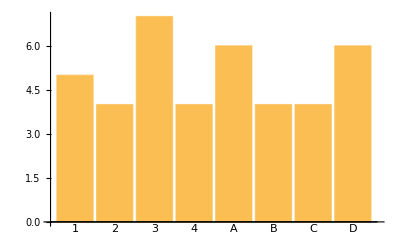

```mathematica
TraitHistogram[population:{___MendelianCreature}]:=Null(* Fill me in *)
```

ExtraCredit: Render the bars using the gene’s individual RGB color contribution. So for example, the latinGenes contributed to the red component in HeredityColor. Therefore, A, B, C and D should be different shades of red. Here’s what ours looks like:

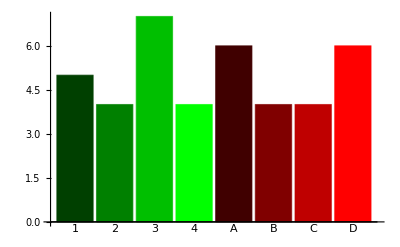

### Tests

#### Verify that HeredityColor of bc1 is GrayLevel of 0.1

```mathematica
ColorConvert[HeredityColor[bc1],"RGB"]===RGBColor[0.1,0.1,0.1]
```

#### Verify that HeredityColor of bc2 is GrayLevel of 0.4

```mathematica
ColorConvert[HeredityColor[bc2],"RGB"]===RGBColor[0.4,0.4,0.4]
```

#### Verify that HeredityColor of mc1

```mathematica
ColorConvert[HeredityColor[mc1],"RGB"]===RGBColor[0.25,0.25,0.]
```

#### Verify that HeredityColor of mc2

```mathematica
ColorConvert[HeredityColor[mc2],"RGB"]===RGBColor[.5,.75,0.]
```

#### Verify that rendering a Blending creature returns a list

```mathematica
MatchQ[Render[bc1],_List]
```

#### Verify that rendering a Mendelian creature returns a list

```mathematica
MatchQ[Render[mc1],_List]
```

#### Verify that rendering a Blending population returns a list

```mathematica
MatchQ[Render[InitializeBlendingPopulation[20]],_List]
```

#### Verify that rendering a Mendelian population returns a list

```mathematica
MatchQ[Render[InitializeMendelianPopulation[20]],_List]
```

#### Verify that we can render a column of graphics for a Blending simulation

This is not an automated test. Eyeball your render and make sure it looks like our render:

```mathematica
Column[{
TraitHistogram[BlendingSimulate[0,20,200][[2]]],
Graphics[Render[BlendingSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

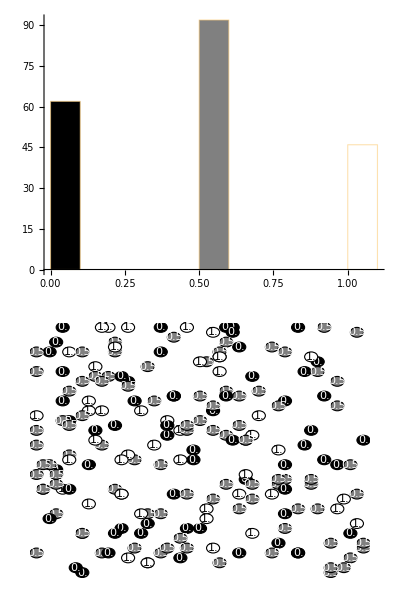

#### Verify that we can render a column of graphics for a Mendelian simulation

This is not an automated test. Eyeball your render and make sure it looks like our render:

```mathematica
Column[{
TraitHistogram[MendelianSimulate[0,20,200][[2]]],
Graphics[Render[MendelianSimulate[0,20,200][[2]]],ImageSize->Large,PlotRange->{{xmin,xmax},{ymin,ymax}},ImagePadding->20]
}, Center]
```

Which should look something like:

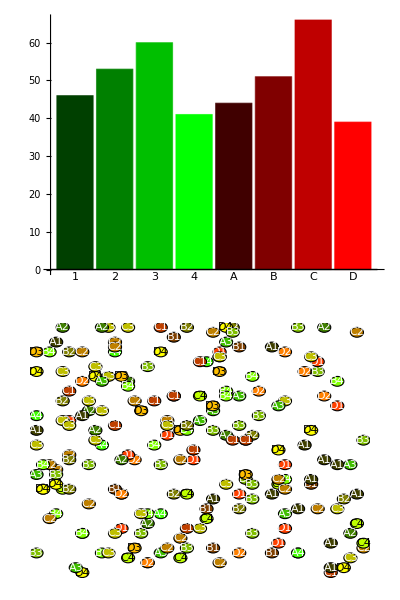

## Manipulate

Here was the Manipulate from part 1:

```mathematica
Manipulate[
Column[{
TraitHistogram[BlendingSimulate[s,20,200][[t]]],
Graphics[Render[BlendingSimulate[s,20,200][[t]]],ImageSize->Large]
},Center],
{{s,0,"Seed"},0,100,1,Appearance->"Open"},
{{t,1,"Generation"},1,20,1,Appearance->"Open",AnimationRate->1}
]
```

Modify it so that you can select between Blending and Mendelian simulations. Hint: remember that we wrote the Simulate function that can be called with a parameter to select between Blending and Mendelian modes.